```mathematica
有限深方势阱
```

```mathematica
Print["r = ",(2*9.11*10^-31*10^-18*2*1.60*10^-19)/(1.0546*10^-34)^2]
```

r = 52.4231

```mathematica
观察奇宇称态的解
```

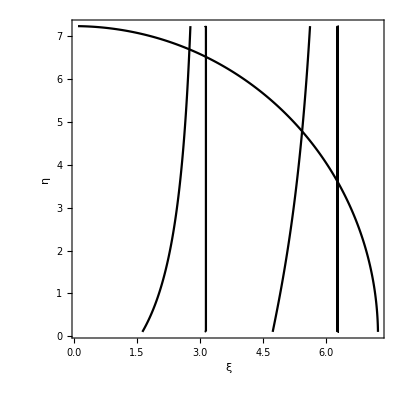

```mathematica
r=52.4231;
ContourPlot[{η+ξ Cot[ξ]==0,η^2+ξ^2==r},
{ξ,0.1,√r},{η,0.1,√r},PlotPoints->200,
FrameLabel->{"ξ","η"},AxesStyle->Thickness[0.003],
ContourStyle->Thickness[0.004]]
Clear[r]
```